```mathematica
makeGraphicsLst[diskLst_]:=
Table[{diskLst[[pos,1]],Disk[diskLst[[pos,2]],0.3]}, {pos,Length@diskLst}]
```

```mathematica
diskLst={{Red, {.5, .5}}, {Blue, {2,2}}, {Orange, {1.5, 2.5}}}
```

{{RGBColor[1, 0, 0],{0.5,0.5}},{RGBColor[0, 0, 1],{2,2}},{RGBColor[1, 0.5, 0],{1.5,2.5}}}

```mathematica
makeGraphicsLst[diskLst]
```

{{RGBColor[1, 0, 0],Disk[{0.5,0.5},0.3]},{RGBColor[0, 0, 1],Disk[{2,2},0.3]},{RGBColor[1, 0.5, 0],Disk[{1.5,2.5},0.3]}}

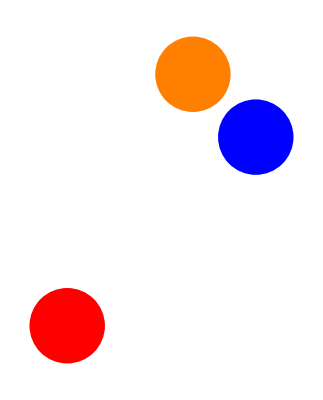

```mathematica
Graphics[%]
```